# Report Project 3

Course code: IX1500
Date: 2024-10-19

Flora Lindberg, floral@kth.se

Task 1: Kruskal’s Algorithm

## Summary

### Task

Uppgiften var att förklara hur Kruskals algoritm fungerar genom att använda Matematicas graf-metoder för att illustrera förklaringen med hjälp av animationer. Förklaringen skulle fokusera på hur algoritmen fungerar snarare än fokus på själva koden över hur algoritmen implementeras.

### Result

Figur 1. Representerar Kruskals algoritm separerad från originalgafen.

Figur 2. Representerar Kruskals algoritm på originalgrafen.

## Formulas and Equations (Updaterad)

### Kruskal.b4s algoritm (Updaterad)

För att få en djupare förståelse för hur algoritmen fungerar så samlades mycket information. Detta gjordes genom att kolla på diverse Youtube-videor kring hur algoritmen fungerar. Utöver så studerades hemsidan “Geeks for geeks” där en tydlig beskrivning över algoritmen fanns. Därutöver hittades en PDF från KTHs kurs “ Problemlösning och programmering under press” som lästes igenom för att få ytterligare kunskap över hur algoritmen fungerade och se så att alla källor stämde överrens.

Enligt “Geeks for geeks” så går Kruskals algoritm ut på att skapa det “billigaste” nätverket. En graf som består av kanter av olika vikt (och hörn), kan sorteras för att få det absolut billigaste nätverket med så låg vikt som möjligt. De skriver att Kruskals algoritm hjälper till att ta fram de absolut billigaste vägarna och att algoritmen baseras i att lägga kanter i olika delmängder för att sedan jämföra dessa med varandra. De berättar även att algoritmen skapar ett “Minimum spanning tree” MST vilket då består av delmängden av de kanter som sammanför alla hörn i grafen med minsta vikt. Det minsta uppspännande trädet (MST) är en figur som består av kanter som sammanför alla hörn i en sammanhöngande graf. Kanterna som sammanför grafen ska ha den absolut lägsta vikten. 

Videon “Union Find Kruskal’s Algorithm” förklarar tydligt att algoritmen utgår ifrån en tabell sorterad med de olika kanternas vikter, med den kortaste vikten först. Den första kantens hörn läggs till i den första delmängden som kan kallas “Rosa”. Hörnen för nästa kant kant i listan jämförs med den rosa delmängden och om det finns ett gemensamt element, läggs kantens hörn till i delmängden och om den inte finns, läggs den till i en ny delmängd. I detta scenario har de inga gemensamma element och den andra kanten läggs in i delmängden “Grön”. Videon visar att nästa kant i grafen kollas först med den första delmängden och om något gemensamt element finns där, så kollas det även om de hörnen till kanten redan finns i delmängden. Om så skulle vara fallet, läggs kanten inte till då detta skulle skapa en cykel. En cykel uppfyller inte kraven för kruskals algoritm och därav kommer inte kanten läggas in.  Om en kant skulle ha ett hörn i två olika delmängder, så kommer dessa två delmängder att sättas ihop och skapa en delmängd tillsammans. När alla hörn är inkluderade, har en väg skapats. 

Koden för den första uppgiften är hårdkodad till följd av att ingen metod skulle göras för själva algoritmen. Inga andra inbyggda funktioner för Kruskals algoritm eller “minimal spanning tree” användes heller.

### Graf för första animationen

```mathematica
Steg 1:
```

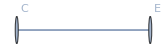

```mathematica
Steg 2:
```

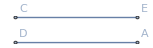

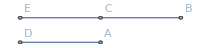

```mathematica
Steg 3:
```

```mathematica
Steg 4:
```

-Graphics-

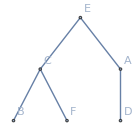

```mathematica
Steg 5:
```

```mathematica
Steg 6:
```

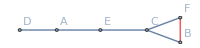

```mathematica
Steg 7:
```

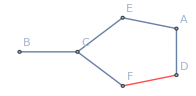

```mathematica
Steg 8:
```

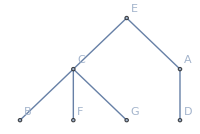

### Graf för andra animationen

```mathematica
Steg 1:
```

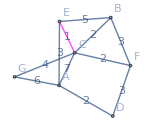

```mathematica
Steg 2:
```

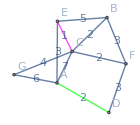

```mathematica
Steg 3:
```

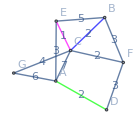

```mathematica
Steg 4:
```

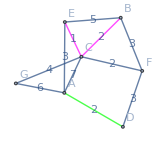

```mathematica
Steg 5:
```

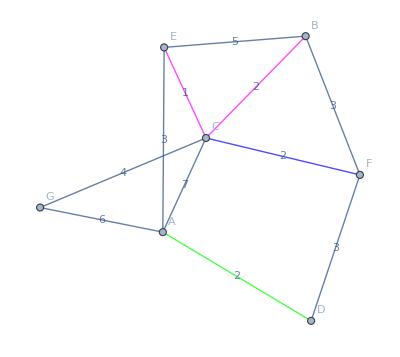
```mathematica
-Graphics-
Steg 6:
```

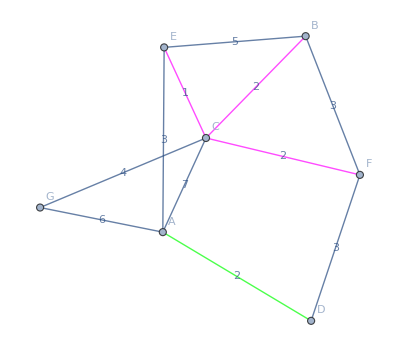
```mathematica
-Graphics-
Steg 7:
```

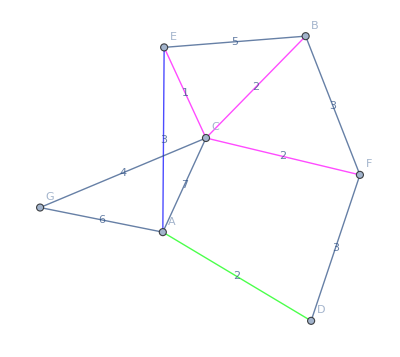
```mathematica
-Graphics-
Steg 8:
```

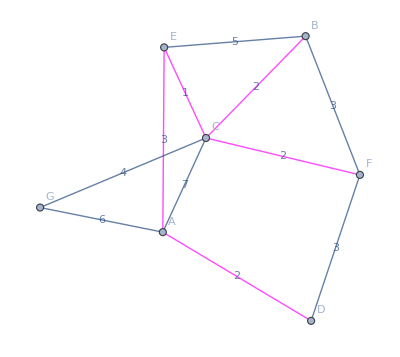
```mathematica
-Graphics-
Steg 9:
```

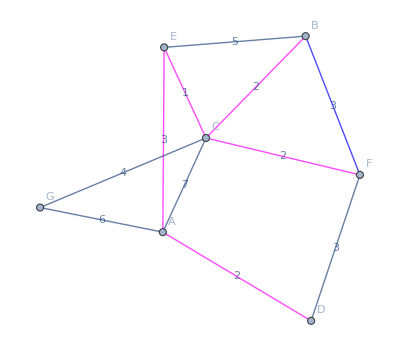
```mathematica
-Graphics-
Steg 10:
```

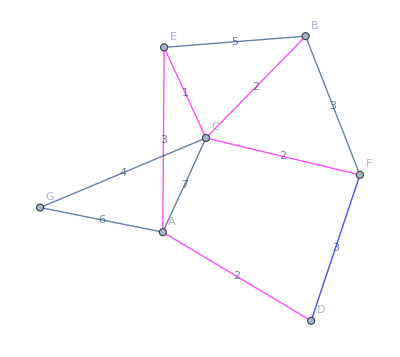
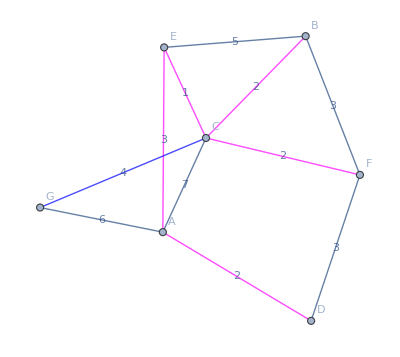
```mathematica
-Graphics-
Steg 11: 
-Graphics-
Steg 12:
```

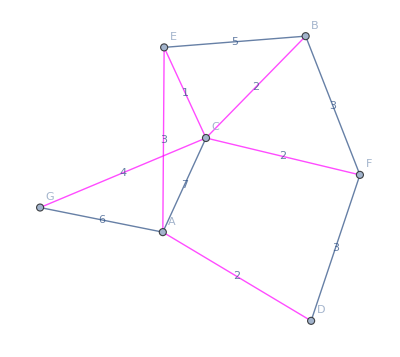
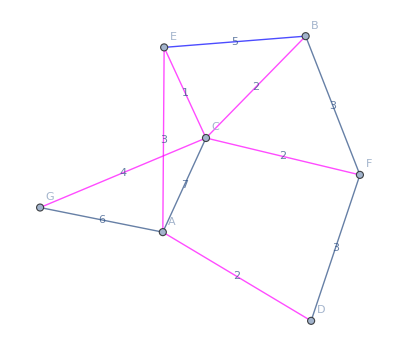
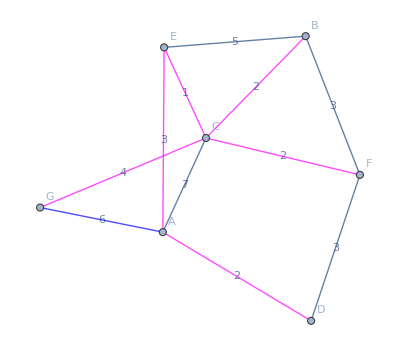
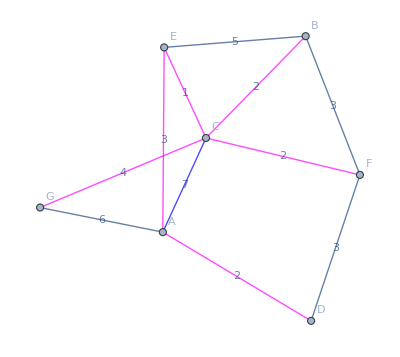
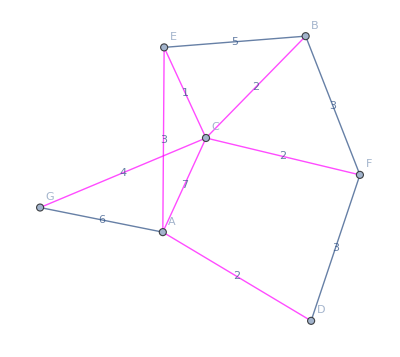
```mathematica
-Graphics-
Steg 13:
-Graphics-
Steg 14:
-Graphics-
Steg 15:
-Graphics-
Steg 16:
-Graphics-
```

## Code

### Kod för första animationen

```mathematica
vertices={"A","B","C","D","E","F","G"};
edges={UndirectedEdge["B","C"]->2,UndirectedEdge["A","D"]->2,UndirectedEdge["B","E"]->5,UndirectedEdge["A","C"] -> 7, UndirectedEdge["B", "F"]->3,  UndirectedEdge["C", "F"]->2,  UndirectedEdge["D", "F"]->3,  UndirectedEdge["C", "G"]->4, UndirectedEdge["A", "G"]->6, UndirectedEdge["A", "E"]->3,UndirectedEdge["C","E"] -> 1};
g=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight"];
edges=EdgeList[g];
sortedEdges=SortBy[edges,PropertyValue[{g,#},EdgeWeight]&];
listOfEdges={};
listedges = {};
nodes={"E","C"};
listedges={UndirectedEdge["E","C"]};
g1=Graph[nodes,listedges,VertexLabels->"Name"];
listOfEdges=edges;
nodes={"E","C","A","D"};
listedges={UndirectedEdge["E","C"],UndirectedEdge["A","D"]};
g2=Graph[nodes,listedges,VertexLabels->"Name"];
listOfEdges=edges;
listedges;
nodes={"E","C","A","D"};
listedges={UndirectedEdge["E","C"],UndirectedEdge["A","D"],UndirectedEdge["B","C"]};
g3=Graph[nodes,listedges,VertexLabels->"Name"];
listOfEdges=edges;
listedges;
nodes={"E","C","A","D","B"};
edges={UndirectedEdge["E","C"],UndirectedEdge["A","D"],UndirectedEdge["B","C"],UndirectedEdge["C","F"]};
g4=Graph[nodes,edges,VertexLabels->"Name"];
nodes={"E","C","A","D","B"};
edges={UndirectedEdge["E","C"],UndirectedEdge["A","D"],UndirectedEdge["B","C"],UndirectedEdge["C","F"], UndirectedEdge["A","E"]};
g5=Graph[nodes,edges,VertexLabels->"Name"];nodes={"E","C","A","D","B","F"};
edges={UndirectedEdge["E","C"],UndirectedEdge["A","D"],UndirectedEdge["B","C"],UndirectedEdge["C","F"], UndirectedEdge["A","E"],UndirectedEdge["B","F"]};
g6=Graph[nodes,edges,VertexLabels->"Name",EdgeStyle->{UndirectedEdge["B","F"]->Red}];
nodes={"E","C","A","D","B","F"};
edges={UndirectedEdge["E","C"],UndirectedEdge["A","D"],UndirectedEdge["B","C"],UndirectedEdge["C","F"], UndirectedEdge["A","E"],UndirectedEdge["D","F"]};
g7=Graph[nodes,edges,VertexLabels->"Name",EdgeStyle->{UndirectedEdge["D","F"]->Red}];
nodes={"E","C","A","D","B","F"};
edges={UndirectedEdge["E","C"],UndirectedEdge["A","D"],UndirectedEdge["B","C"],UndirectedEdge["C","F"], UndirectedEdge["A","E"],UndirectedEdge["C","G"]};
g8=Graph[nodes,edges,VertexLabels->"Name"];
{"B"<->"E","A"<->"G","A"<->"C"};
Manipulate[Which[n==1,g,n==2,g1,n==3,g2,n==4,g3,n==5,g4,n==6,g5,n==7,g6,n==8,g7, n==9,g8],{{n,1,"Select Graph"},1,9,1,Appearance->"Labeled"}];
```

### Kod för andra animationen

```mathematica
vertices={"A","B","C","D","E","F","G"};
edges={UndirectedEdge["B","C"]->2,UndirectedEdge["A","D"]->2,UndirectedEdge["B","E"]->5,UndirectedEdge["A","C"] -> 7, UndirectedEdge["B", "F"]->3,  UndirectedEdge["C", "F"]->2,  UndirectedEdge["D", "F"]->3,  UndirectedEdge["C", "G"]->4, UndirectedEdge["A", "G"]->6, UndirectedEdge["A", "E"]->3,UndirectedEdge["C","E"] -> 1};
graph1=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta}];
graph2=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Green}];
graph3=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Green,UndirectedEdge["B","C"]->Blue}];
graph4=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Green,UndirectedEdge["B","C"]->Magenta}];
graph5=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Green,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Blue}];
graph6=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Green,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta}];
graph7=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Green,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Blue}];
graph8=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Magenta,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Magenta}];
graph9=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Magenta,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Magenta,UndirectedEdge["B","F"]->Blue}];
graph10=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Magenta,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Magenta,UndirectedEdge["D","F"]->Blue}];
graph11=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Magenta,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Magenta,UndirectedEdge["C","G"]->Blue}];
graph12=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Magenta,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Magenta,UndirectedEdge["C","G"]->Magenta}];
graph13=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Magenta,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Magenta,UndirectedEdge["C","G"]->Magenta,UndirectedEdge["B","E"]->Blue}];
graph14=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Magenta,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Magenta,UndirectedEdge["C","G"]->Magenta,UndirectedEdge["A","G"]->Blue}];
graph15=Graph[vertices,Keys[edges],EdgeWeight->Values[edges],VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeStyle->{UndirectedEdge["E","C"]->Magenta,UndirectedEdge["A","D"]->Magenta,UndirectedEdge["B","C"]->Magenta,UndirectedEdge["C","F"]->Magenta,UndirectedEdge["A","E"]-> Magenta,UndirectedEdge["C","G"]->Magenta,UndirectedEdge["A","C"]->Blue}];
Manipulate[Which[n==1,g,n==2,graph1,n==3,graph2,n==4,graph3,n==5,graph4,n==6,graph5,n==7,graph6,n==8,graph7,n==9,graph8,n==10,graph9,n==11,graph10,n==12,graph11,n==13,graph12,n==14,graph13,n==15,graph14,n==16,graph15],{{n,1,"Select Graph"},1,16,1,Appearance->"Labeled"}];
```

Task 2: Relationer mellan städer

## Summery

### Task

I uppgiften skulle olika städer representera en router som vidareskickar datapaket för att kunna nå deras slutdestination. Uppgiften var att skapa ett träd som visar hur paketen skickas så att varje stad kan nås av informationsflödet som baseras i Stockholm.

### Result

#### Grafer och kartor

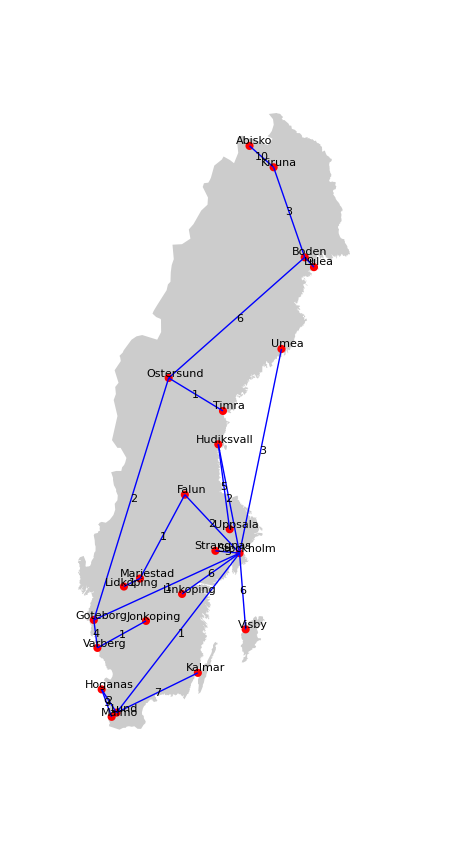
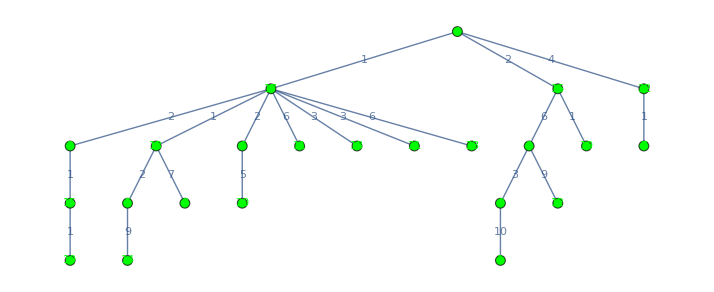

#### Dijkstras algoritm för att lösa problemet

Funktionen FindShortestPath som användes för att ta fram sträckan med den lägsta vikten liknar den algoritm som heter Dijkstras algoritm som just går ut på att hitta den lägsta vikten mellan hörn. Genom att jämföra olika sträckor och vikt mellan varandra så hittar funktionen den väg med den lägsta vikten. Algoritmen jämför således de olika möjligheterna  att ta sig från ett hörn till ett annat genom att kolla på det hörn som inte använts tidigare och med lägsta vikt. Därefter beräknar den avståndet till obesökta grannhörn och updaterar sträckan om den är billigare än en annan väg.

#### Om länken Göteborg - Lund slutar fungera

Om länken mellan Göteborg - Lund skulle sluta fungerar så skulle det inte leda till någon större konsekvens för informationsflödet. Den givna kapaciteten mellan Göteborg-Lund var 25 vilket betydde att vikten resulterade i 30/25 och avrundades till 1. Sträckan mellan Stockholm-Göteborg hade även denna vikten 1 och även Stockholm-Lund. Detta ledde till att det inte blev några städer som hade påverkats av att sträckan Göteborg-Lund hade slutat fungera. Om informationen ska skickas till Varberg så går det från Stockholm via Göteborg och till Kalmar går det via Lund. Det kommer därav inte finnas några städer som blir påverkade eftersom den sträckan endast skulle leda till en extra vikt. 

Hade det däremot varit sträckan Stockholm - Göteborg så hade flera andra städer blivit påverkade eftersom Göteborg är ett hörn som leder ut till andra hörn från Stockholm. Då hade även städerna Östersund, Boden, Luleå, Kiruna och Abisko, Varberg och Jönköping blivit påverkade. Då hade denna sträcka behövt bli borttagen från uträkningen så att någon av de många andra alternativen blivit valda till kartan istället. Alternativt hade samma uträkning kunnat användas men ändra vikten på sträckan Stockholm - Göteborg till ett otroligt högt värde vilket hade lett till att algoritmen aldrig hade valt den vägen.

## Formulas and Equations

### Metod

Det första som gjordes var att dela upp de olika relationerna mellan städerna så att de sträckorna med förbestämda kapaciteter inte skulle få slumpmässigt genererade kapaciteter. De sträckorna med förbestämda kapaciteter lades i en separat lista och deras respektive vikter beräknades genom att använda konstanten 30 dividerat på de olika konstanterna. Därefter ritades den graf upp som representerade sträckorna och städerna. För att generera vikter till de övriga sträckorna så togs först komplementet av listan med all sträckorna och listan av de förbestämda sträckorna fram. Dessa var således de sträckor som skulle få de slumpmässigakapaciteterna. Kapaciterna togs fram genom att använda “RandomInteger” i intervallet 1-10 och därefter genererades lika många tal som antalet sträckor som skulle ha slumpmässiga kapaciteter. För att sedan skapa vikterna till ströckorna användes återigen konstanten satt till 30. En ny lista skapades där de olika kapaciterna delade konstanen 30 för att få fram vikterna. För att sedan kunna ge de olika ströckorna de olika vikterna, en graf skapades där det första elementet i listan med komplementet, matchades med den första vikten i listan. Därefter skapades en graf för att visuellt kunna se de olika sträckorna och dess viktor för att säkerställa att resultatet stämde. I koden har dessa slumpmässiga tal lagts in som en lista för att kunna använda samma värden för varje test under processen.

 För att sedan slå samman dessa två grafer så skapades två nya variabler “totalEdges” och “totalWeight” där de olika två slogs samman. När det fanns en sammanslagen graf så togs en “viktad grannmatris” fram för att senare kunna använda de olika vikterna mellan sträckorna. För att kunna skapa ett träd med minsta vikt  med Stockholm som utgångspunkt, användes funktionen “Find Shortest Path”. Då gjordes en For-loop för att kunna gå igenom alla möjliga vägar för att ta sig från Stockholm till alla andra städer. Dessa vägar lades in i en lista. För att skapa ett träd så behövde vissa vägar sorteras bort eftersom det fanns flera vägar som delade en viss sträcka innan de delade på sig och gick åt separata håll. Detta gjordes genom att först sortera listan så att den absolut längsta vägen hamnade först i listan. Därefter gjordes en For-loop som kollade om det fanns några äkta delmängder eftersom detta skulle betyda att det var en väg som skulle läggas till i listan.  Därför var det viktigast att den längsta vägen lades in först i listan så att de äkta delmängderna skulle börja jämföras med detta elementet. För att göra det möjligt att få fram de olika vikterna mellan de olika städerna så behövde en lista med kanterna tas fram. Då kunde även de respektive vikterna fås och dessa kunde sedan sättas ihop till ett träd. 
 
 För att därefter placera dessa på kartan över Sverige så användes de givna metoderna från uppgiften. Kooridnaterna för alla städer togs fram tillsammans med alla hörn och kanter från den slutgiltiga grafen. När allting sattes in så visades kartan över Sverige med de olika transportsträckorna för informationsflödet. De olika sträckorna jämfördes med den första grafen där alla sträckor och vikter visades och därefter bekräftades det att kartan hade den lägsta vikten.

### Grafer och matriser

Ekvation för att beräkna de olika vikterna.

K/n   K = 30, n representerar de slumpmässigt genererade heltalen.

Lista med vikterna genererade av slumpmässiga kapaciteter.

```mathematica
{6,10,5,9,2,4,2,9,7,1,1,4,10,3,7,3,8,8,9,9,2,7,7,1,1,7,8,2,4,10,8,5,1,6,6,10,3,7,7,7,4,5,9,3,4,4}
```

Graf för de sträckor med förbestämda kapaciteter.

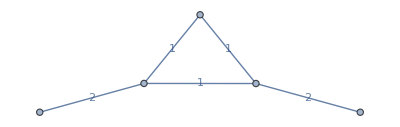

Graf för de sträckor med slumpmässiga kapaciteter.

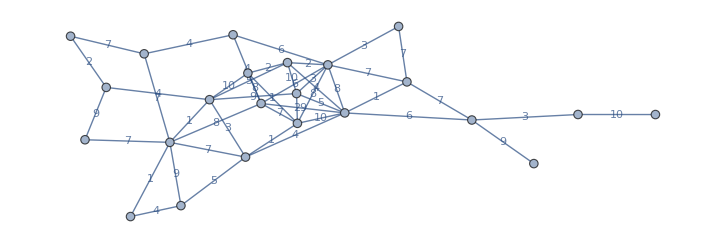

Sammansatt graf förförbestämda och slumpmässiga.

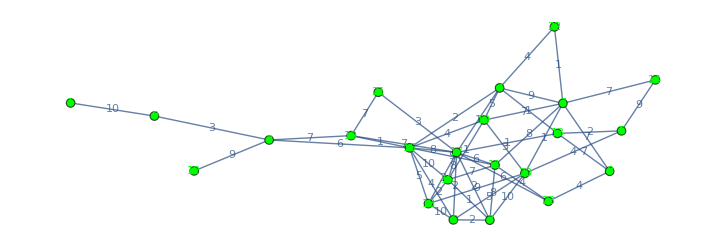

"Weighted adjacency matrix" (viktad grannmatris) för den sammansatta grafen.

(0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 9 | 0 | 0 | 0 | 7 | 0
6 | 0 | 0 | 0 | 2 | 4 | 0 | 0 | 4 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 10 | 5 | 1 | 0
0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 8 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 10 | 0 | 0 | 3 | 4 | 0 | 5 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0
0 | 2 | 0 | 0 | 0 | 5 | 0 | 0 | 0 | 1 | 9 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 4 | 0 | 3 | 5 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 2 | 5 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0
0 | 8 | 2 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 1 | 8 | 3 | 7 | 3
0 | 0 | 0 | 1 | 9 | 7 | 0 | 7 | 0 | 0 | 0 | 7 | 1 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 4 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 8 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 1 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 10 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 8 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 2 | 0 | 0
0 | 5 | 0 | 9 | 0 | 0 | 0 | 0 | 10 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7 | 0)

Karta med den sammansatta grafen.

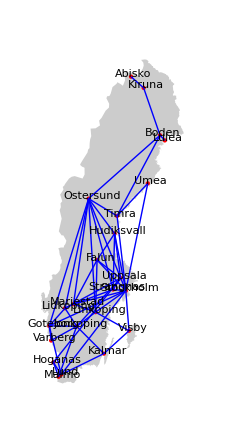

De olika vägarna mellan Stockhol och alla övriga städer

Vägen mellan 17 och 1: {17,4,16,2,9,1}

Vägen mellan 17 och 2: {17,4,16,2}

Vägen mellan 17 och 3: {17,3}

Vägen mellan 17 och 4: {17,4}

Vägen mellan 17 och 5: {17,13,5}

Vägen mellan 17 och 6: {17,6}

Vägen mellan 17 och 7: {17,4,22,7}

Vägen mellan 17 och 8: {17,13,8}

Vägen mellan 17 och 9: {17,4,16,2,9}

Vägen mellan 17 och 10: {17,3,15,10}

Vägen mellan 17 och 11: {17,11}

Vägen mellan 17 och 12: {17,4,16,2,12}

Vägen mellan 17 och 13: {17,13}

Vägen mellan 17 och 14: {17,13,5,14}

Vägen mellan 17 och 15: {17,3,15}

Vägen mellan 17 och 16: {17,4,16}

Vägen mellan 17 och 17: {17}

Vägen mellan 17 och 18: {17,18}

Vägen mellan 17 och 19: {17,4,16,19}

Vägen mellan 17 och 20: {17,6,20}

Vägen mellan 17 och 21: {17,21}

Vägen mellan 17 och 22: {17,4,22}

Vägen mellan 17 och 23: {17,23}

Slutgiltiga vägar.

```mathematica
{{17,4,16,2,9,1},{17,4,16,2,12},{17,13,5,14},{17,4,22,7},{17,4,16,19},{17,3,15,10},{17,13,8},{17,6,20},{17,23},{17,21},{17,18},{17,11}}
```

## Code

```mathematica
city={"Abisko","Boden","Falun","Goteborg","Hoganas","Hudiksvall","Jonkoping","Kalmar","Kiruna","Lidkoping","Linkoping","Lulea","Lund","Malmo","Mariestad","Ostersund","Stockholm","Strangnas","Timra","Uppsala","Umea","Varberg","Visby"};
links={{15,18},{13,17},{3,16},{6,3},{18,6},{12,2},{15,11},{19,21},{7,8},{19,2},{7,4},{21,17},{17,11},{23,11},{10,7},{16,17},{10,20},{13,5},{3,17},{7,22},{15,10},{16,18},{11,16},{17,23},{18,17},{20,6},{11,7},{9,2},{3,20},{4,17},{19,17},{7,20},{22,4},{14,7},{15,17},{6,17},{20,5},{16,15},{11,3},{9,1},{4,10},{5,14},{6,16},{16,19},{13,8},{8,23},{16,10},{4,13},{2,16},{15,3},{20,18}};
```

```mathematica
exclude ={{4,17},{13,17},{4,13},{3,17},{3,16}};
```

```mathematica
excluded=Graph[{UndirectedEdge[4,17],UndirectedEdge[13,17],UndirectedEdge[4,13],UndirectedEdge[17,3],UndirectedEdge[4,16]},EdgeWeight->{Round[(30/25)],Round[(30/25)],Round[(30/25)],(30/15),Round[(30/15)]},EdgeLabels->"EdgeWeight"];
```

```mathematica
excludedWeigth={Round[(30/25)],Round[(30/25)],Round[(30/25)],(30/15),Round[(30/15)]};
```

```mathematica
listComplement=Complement[links,exclude];
```

```mathematica
capacities=RandomInteger[{1,10},Length[listComplement]];
weights=Round[30/capacities];
```

```mathematica
excludeGraph= Graph[listComplement, EdgeWeight->{6,10,5,9,2,4,2,9,7,1,1,4,10,3,7,3,8,8,9,9,2,7,7,1,1,7,8,2,4,10,8,5,1,6,6,10,3,7,7,7,4,5,9,3,4,4},EdgeLabels-> "EdgeWeight"];
```

```mathematica
weigthex= {6,10,5,9,2,4,2,9,7,1,1,4,10,3,7,3,8,8,9,9,2,7,7,1,1,7,8,2,4,10,8,5,1,6,6,10,3,7,7,7,4,5,9,3,4,4};
```

```mathematica
totalEdges = Join[EdgeList[excludeGraph],EdgeList[excluded]];
totalWeigth = Join[weigthex,excludedWeigth];
totalGraph= Graph[totalEdges, EdgeWeight->totalWeigth,EdgeLabels-> "EdgeWeight",VertexLabels->Placed["Name",Center],VertexStyle->Green];
```

```mathematica
adjMatrix=WeightedAdjacencyMatrix[totalGraph];
MatrixForm[adjMatrix];
```

```mathematica
paths={};  
For[i=1,i<24,i++,path=FindShortestPath[totalGraph,17,i];
paths=Append[paths,path]; ]
paths;
```

```mathematica
paths2=Reverse[SortBy[paths,Length]];
```

```mathematica
subsetPaths={};
For[i=1,i<=Length[paths],i++,If[!AnyTrue[subsetPaths,SubsetQ[#,paths2[[i]]]&],subsetPaths=Append[subsetPaths,paths2[[i]]]]]
subsetPaths;
```

```mathematica
edges={};
For[i=1,i<=Length[subsetPaths],i++,currentPath=subsetPaths[[i]];
For[j=1,j<Length[currentPath],j++,AppendTo[edges,UndirectedEdge[currentPath[[j]],currentPath[[j+1]]]];]]
edges;
```

```mathematica
subsetEdges={};
For[i=1,i<=Length[edges],i++,If[!AnyTrue[subsetEdges,SubsetQ[#,edges[[i]]]&],subsetEdges=Append[subsetEdges,edges[[i]]]]];
```

```mathematica
subsetEdges;
```

```mathematica
weigthList={}; 
For[i=1,i<=Length[subsetEdges],i++,currentNode=subsetEdges[[i]];weight=PropertyValue[{totalGraph,currentNode},EdgeWeight];weigthList=Append[weigthList,weight]; ]
```

```mathematica
finishedGraph=Graph[subsetEdges,EdgeWeight-> weigthList,EdgeLabels-> "EdgeWeight",VertexLabels->Placed["Name",Center],VertexStyle->Green];
```

```mathematica
vlist=VertexList[finishedGraph];
elist=EdgeList[finishedGraph];
flo=Table[CityData[city⟦i⟧,"Coordinates"],{i,Length[city]}];
Options[geoGraph]={
EdgeStyle->Black,EdgeLabels->"EdgeWeigth",VertexStyle->GeoStyling[None],
VertexLabels->None,VertexLabelStyle->Black
};
geoGraph[v_,e_,c_,r_,OptionsPattern[]]:=
Module[{
es=OptionValue[EdgeStyle],vs=OptionValue[VertexStyle],vl=OptionValue[VertexLabels],vls=OptionValue[VertexLabelStyle],
lbl,Δ={0.1,0.3}
},
If[Length[vl]≠Length[v],vl=None];
lbl=If[
vl===None,{},
Join[{vls},MapThread[Text[#1,GeoPosition[#2+Δ],{-1,0}]&,{vl,c}]]
];
Join[
Join[{vs},(GeoDisk[c⟦#1⟧,r]&)/@v],
Join[{es},(GeoPath[{c⟦#1⟦1⟧⟧,c⟦#1⟦2⟧⟧}]&)/@e],
lbl
]
]
r=10 *10^3;
GeoGraphics[{
Polygon[CountryData["Sweden"]],
geoGraph[vlist,elist,flo,r,EdgeStyle->Blue,EdgeLabels->"EdgeWeigth", VertexStyle->GeoStyling[Red],VertexLabels->city]
},GeoBackground->None,GeoProjection->"LambertAzimuthal"];
```

## Diskussion

Det var en mycket intressant uppgift där olika algoritmer fick utrymme att användas vilket var väldigt lärorikt. Den första uppgiften var intressant då den bidrog till en större förståelse för Mathematicas graf-fuktioner och även funktioner för animering. Det blev mycket tydligare hur deras inbyggda funktioner kan användas för att demonstrera och illustrera något tydligt. Det var även uppskattat att det fanns två olika uppgifter att välja på vilket bidrog till att det fanns tillfälle att fokusera på det område som krävde extra träning. Den andra uppgiften var också lärorikt då en större förståelse skapades för hur detta kan användas för reella problem. Dock var intruktionerna delvis otydliga och inte så specifika vilket gjorde att mycket tid gick åt att tolka instruktionen för att veta vad som förväntades.  Överlag var det en rolig och intressant uppgift där mer förståelse skapades för olika algoritmer och grafer.

Dela upp i lista

## Källförteckning (ny)

Henrik Sjögren, Jesper Hjertstedt. Föreläsning 12: Önskekonsert. PDF - KTH. https : // www.csc. kth. se/utbildning/kth/kurser/DD2458/popup06/dokument/F12/F12 . pdf . 2006-12-04.  Hämtad 2024-10-25.

William Fiset. Union Find Kruskal’s Algorithm. Youtube: https://www.youtube.com/watch?v=JZBQLXgSGfs. Hämtad 2024-10-25. 

Geeks for geeks. Kruskal’s Minimum Spanning Tree (MST) Algorithm.  https://www.geeksforgeeks.org/kruskals-minimum-spanning-tree-algorithm-greedy-algo-2/ 2023-10-05. Hämtad 2024-10-25.